```mathematica
计算3个点电荷的电力线-事件探测器法
```

NDSolve::evre: The value of the event function at TraditionalForm`t = TraditionalForm`1.0042358628693883`*^-14 was not a real number. The event will be ignored in steps where it does not evaluate to real numbers at both ends.

NDSolve::ndsz: At TraditionalForm`t == TraditionalForm`145.32768544703413`, step size is effectively zero; singularity or stiff system suspected.

NDSolve::evre: The value of the event function at TraditionalForm`t = TraditionalForm`1.0163685039496376`*^-14 was not a real number. The event will be ignored in steps where it does not evaluate to real numbers at both ends.

NDSolve::ndsz: At TraditionalForm`t == TraditionalForm`504.1415413145253`, step size is effectively zero; singularity or stiff system suspected.

NDSolve::evre: The value of the event function at TraditionalForm`t = TraditionalForm`1.0544954976490564`*^-14 was not a real number. The event will be ignored in steps where it does not evaluate to real numbers at both ends.

General::stop: Further output of NDSolve :: evre will be suppressed during this calculation.

NDSolve::ndsz: At TraditionalForm`t == TraditionalForm`163.3175731137672`, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

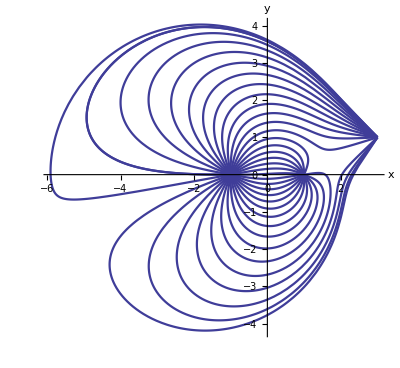

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
(*.........................*)
p1={1,0};p2={-1,0};p3={3,1};r=10.0^-3;
q1=1.0;q2=-2.0;q3=5.0;forceline={};
ψ=q1/(√((x-1)^2+y^2))+q2/(√((x+1)^2+y^2))+
q3/(√((x-3)^2+(y-1)^2));
ex[t_]:=Evaluate[D[ψ,x]/.{x->x[t],y->y[t]}]
ey[t_]:=Evaluate[D[ψ,y]/.{x->x[t],y->y[t]}]
equ={x'[t]==ex[t],y'[t]==ey[t],
x[0]==x0,y[0]==y0};
Do[
{x0,y0}=p2+r {Cos[ϕ],Sin[ϕ]};
s=NDSolve[equ,{x,y},{t,0,∞},
Method->{"EventLocator",
"Event"->Norm[{x[t],y[t]}-p1]-r∨
Norm[{x[t],y[t]}-p3]-r}];
end = InterpolatingFunctionDomain[
First[y/.s]][[1,-1]];
g=ParametricPlot[
Evaluate[{x[t], y[t]} /. First[s]],
 {t,0,end}, PlotStyle->Thickness[0.004]];
AppendTo[forceline,g],
{ϕ,-π,π,π/18.0}]
Show[forceline,PlotRange->All,
AxesStyle->Thickness[0.003],
AxesLabel->{"x","y"},
BaseStyle->{FontSize->13}]
Clear[ψ,ex,ey,x0,y0,x,y]
```